```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["LECS.dat","Table"]
```

{{#,(ecce),the,3-body,LECs,are,renormalized,to,a,constant,B(3,groundstate)=8.48MeV,for,*all*,dimer,binding,energies},{#,L[fm^-1],C_0[b2=0.5],C_0[b2=1.0],C_0[b2=2.22],C_0[b2=5],C_0[b2=7],C_0[b2=10],D_0[b2=0.5],D_0[b2=1.0],D_0[b2=2.22],D_0[b2=5],D_0[b2=7],D_0[b2=10]},{4,-473.112,-484.931,-505.095,-536.711,-554.536,-577.478,668.05,862.333,1388.44,4578.68,23236.7,0.},{6,-701.891,-716.237,-740.666,-778.775,-800.166,-827.603,1305.54,1678.41,2823.86,11401.4,99525.4,0.},{8,-929.686,-946.182,-974.213,-1017.79,-1042.21,-1073.41,2100.03,2764.11,4864.62,26594.4,302419.,0.},{10,-1156.86,-1175.25,-1206.45,-1254.86,-1281.9,-1316.46,2928.63,4149.54,7686.28,50852.,906370.,0.}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2,bd_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

(* in the LEC table, col 2:C(0.5)  3:C(1.0)  4:C(2.22)  5:C(5)  6:C(7)  8:C(10) 
                   col 9:D(0.5) 10:C(1.0) 11:C(2.22) 12:C(5) 13:C(7) 14:C(10)*)
LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[bd]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Ns,Nd}];*)
widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-12.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =(π^(3/2)/4) Cc/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];
(*AppendTo[Wmats,cij amat];*)

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
Print["relative error in wave-function solution = ",relerr];

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

-1281.9

λ = 10   C_0(λ) = -1281.9  #(width-set candidates) = 39708  in 4 parallel threads.

Core 2 : -6.79493{{0.058855,0.14021},{0.133287,0.5311},{0.10183,1.3235},{0.413921,3.088},{0.892788,13.597}}

Core 4 : -6.71737{{0.0390828,0.11865},{0.0970678,0.33493},{0.184688,1.2121},{0.354426,3.0252},{0.910672,12.887}}

Core 3 : -6.81434{{0.0507578,0.11782},{0.183824,0.5824},{0.0657413,2.1308},{0.409738,3.0451},{0.889621,13.669}}

Core 1 : -6.53423{{-0.0421865,0.15254},{-0.0735497,0.22892},{-0.355575,1.3137},{-0.345291,5.0772},{-0.864379,12.981}}

optimum of 39708 candidate width sets found in Δt = 8.94213 sec.          : E_0 = -6.81434

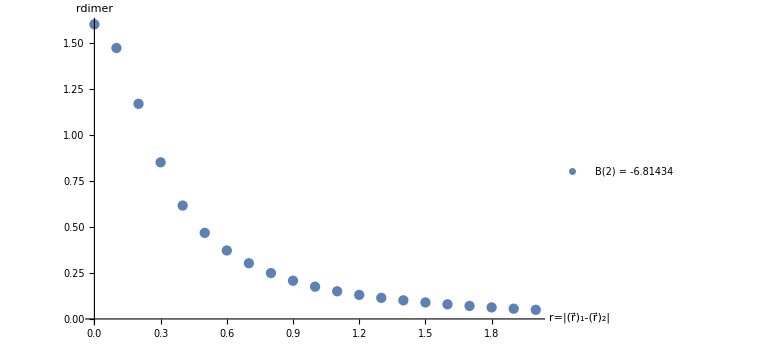

```mathematica
flag=1;

lambdaTest=10;
(* bdtest = 2:C(0.5)  3:C(1.0)  4:C(2.22)  5:C(5)  6:C(7)  8:C(10)*)
bdtest=6;
dimD=5;
minW=0.1;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[bdtest]];
dCores={};

ncc=1;
If[flag>0,
Do[
{eDi,wDi}=ApproxDimerWF[lambdaTest,dimD,4,10000,minW,Random[Real,{8,21}],0.005,1,1,bdtest];
AppendTo[dCores,{eDi,wDi}];
,{nc,Range[ncc]}];
];

If[flag>=0,
NormTF[#]&/@dCores[[All,2]];

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]];

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

{{-6.96349,{{0.0165382,0.062374},{0.0898728,0.21804},{0.293015,0.963583},{0.595126,4.41712},{0.704065,14.0786},{0.23645,29.2893}}}}

{{0.,1.},{0.1,0.818731},{0.2,0.67032},{0.3,0.548812},{0.4,0.449329},{0.5,0.367879},{0.6,0.301194},{0.7,0.246597},{0.8,0.201897},{0.9,0.165299},{1.,0.135335},{1.1,0.110803},{1.2,0.090718},{1.3,0.0742736},{1.4,0.0608101},{1.5,0.0497871},{1.6,0.0407622},{1.7,0.0333733},{1.8,0.0273237},{1.9,0.0223708},{2.,0.0183156}}

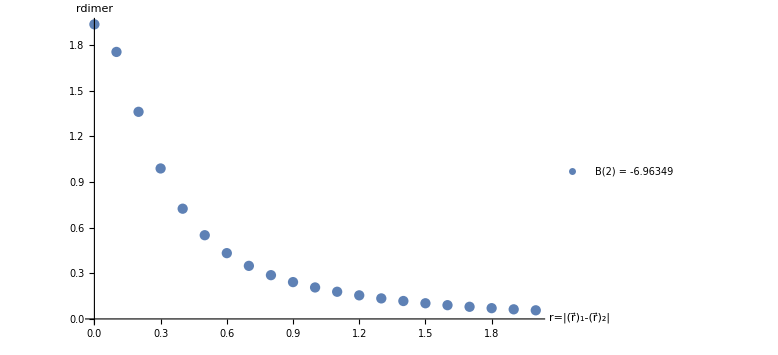

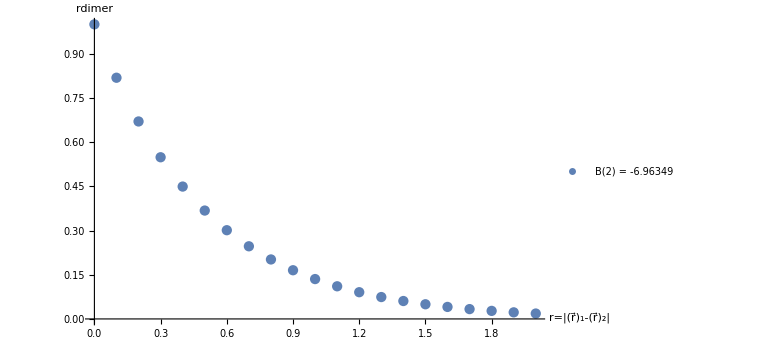

```mathematica
(* bdtest = 2:C(0.5)  3:C(1.0)  4:C(2.22)  5:C(5)  6:C(7)  8:C(10)*)
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[bdtest]];
wCores={Reverse[{29.289293,14.078578,4.417118,0.963583,0.218040,0.062374}]};

If[flag>=0,

dCores=CalcDimerE[#,lambdaTest,LECc]&/@wCores]

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;
plotDataExp=Table[{rr,Exp[-2 rr]},{rr,rR}]

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;

ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic]
ListPlot[plotDataExp,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic]
```

```mathematica
dCores={{0.43,{{0.685124131176013,4.227583924995803},{-1.4012581653447682,2.929412217424905},{0.9104377137581138,2.179357041637498},{0.8056963204138828,0.06172298393588396}}}};
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.95;
(* Integration grid *)
rMa=8;
grdPerFermi=10;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
(*{e0Core,dimerCore}=dCores[[nn]];*)
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,{1}}];
```

relative error in wave-function solution = 3.21586×10^-16

finite-difference runtime Δt = 0.0322847 mins     p_match·r_max = 1.7123

core 1 )  λ=10 ; C_0(λ)=-1156.86 ; R_max=8 ; #=80 ; E_match=0.95 ; B(2)=0.43 ; dim_d=4 ; a_dd=7.07038 ; a_dd/a_aa=0.71993

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

relative error in wave-function solution = 3.27396×10^-16

finite-difference runtime Δt = 0.0473567 mins     p_match·r_max = 3.63864

core 1 )  λ = 10   C_0(λ) = -1156.86     R_max = 17.     #(grid points) = 102                a_dd = 7.67704 fm        a_dd/a_aa = 0.781702

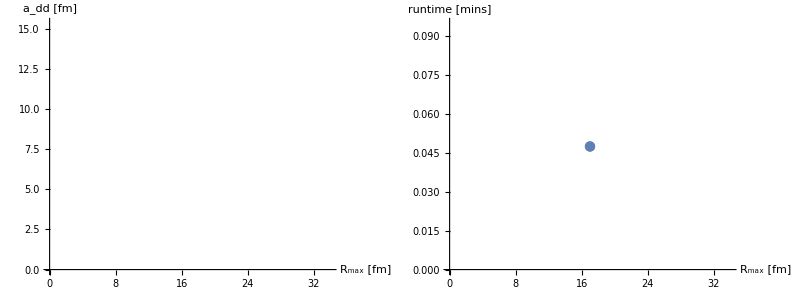

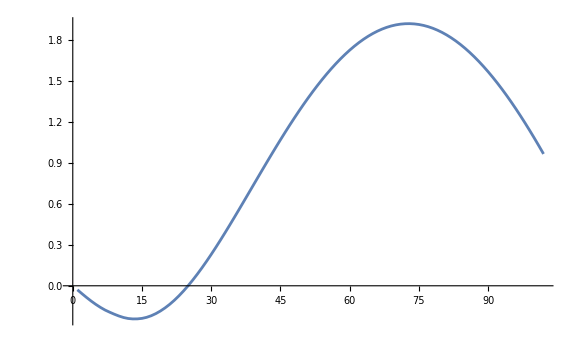

```mathematica
grdPerFermi=6;
rMaxStart=17;
rMaxEnd=17;
nbrR=1;
coreNBR=1;
{e0Core,dimerCore}=dCores[[coreNBR]];
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```

{{nm→1.05796,tandd→-1.51845}}

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

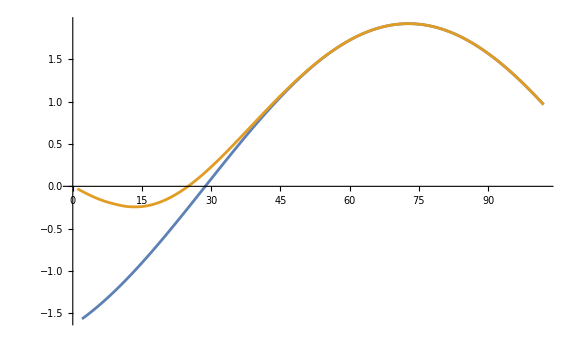

a_dd = 7.09432     a_dd/a_aa = 0.722368

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMaxEnd,1/grdPerFermi];
match1=1;
match2=5;

sol=NSolve[{resultsWF[[-1]][[-match1]]==nm (RiccatiBesselJ[momFM (rMaxEnd-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMaxEnd-match1/grdPerFermi),0]),
resultsWF[[-1]][[-match2]]==nm (RiccatiBesselJ[momFM (rMaxEnd-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMaxEnd-match2/grdPerFermi),0])},{nm,tandd},Reals]

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
ListPlot[{RiccatiBJN[[;;-2]],resultsWF[[-1]]},Joined->True,PlotRange->Full,ImageSize->Large]
add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbar/√(Mm Abs[e0Core])) ]
```

λ = 8 fm^-2  non-local

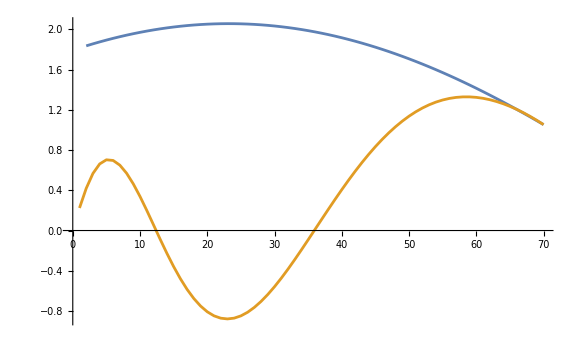

a_dd = -8.50457     a_dd/a_aa = -1.29223

λ = 8 fm^-2  local

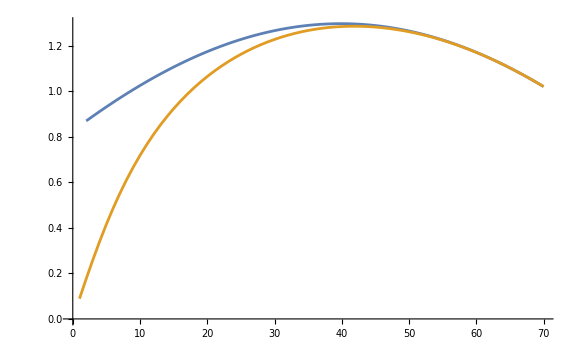

a_dd = -3.91756     a_dd/a_aa = -0.595254

EFT parameters | Numerical parameters | plot control
cutoff regulator λ = 10 | R_max = 17 | #(plot grid points) = 40
C_0(λ) = -1156.86 | #(Integration grid points) = 51 | plot threshold =  0.001
B(2) = 0.43 | dimer-basis dimension = 4 |

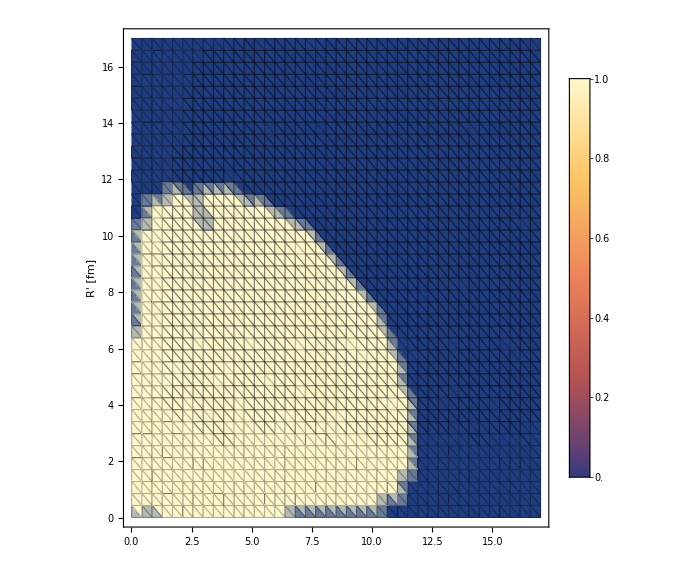
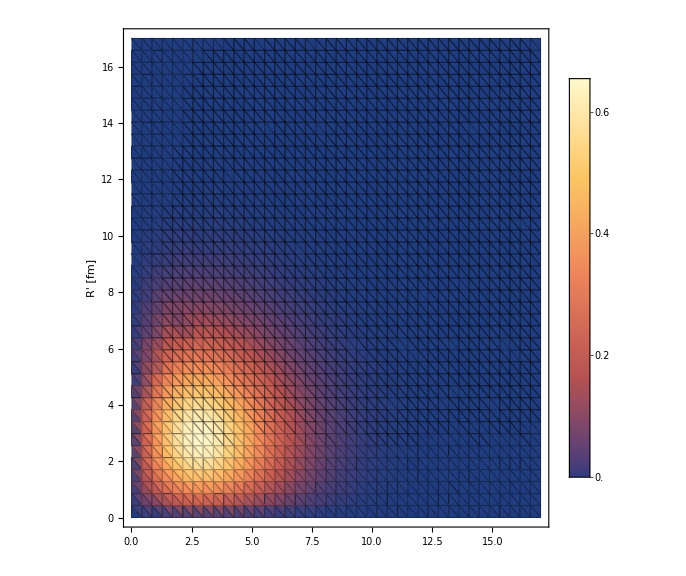
-Graphics- | -Graphics-

```mathematica
(* Integration grid *)
rMa=rMaxEnd;
grdPerFermi=3;
nGrd=IntegerPart[rMa grdPerFermi];

(* Plot parameters for the visualization of V(r,r') *)
nR=40;rMi=0.01;thresh=10^-3;

normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Grid[{{"EFT parameters","Numerical parameters","plot control"},{"cutoff regulator λ = "<>ToString[lambdaTest],"R_max = "<>ToString[rMa],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc],"#(Integration grid points) = "<>ToString[nGrd],"plot threshold = "NumberForm[N[thresh]]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All]

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];

potnoloc3d={};
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;
potnoloc3dtmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],mh2 cij WnolocTF3[rR[[i]],rR[[j]],energ,lambdaTest,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=thresh,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```

w/o  small  widthpara

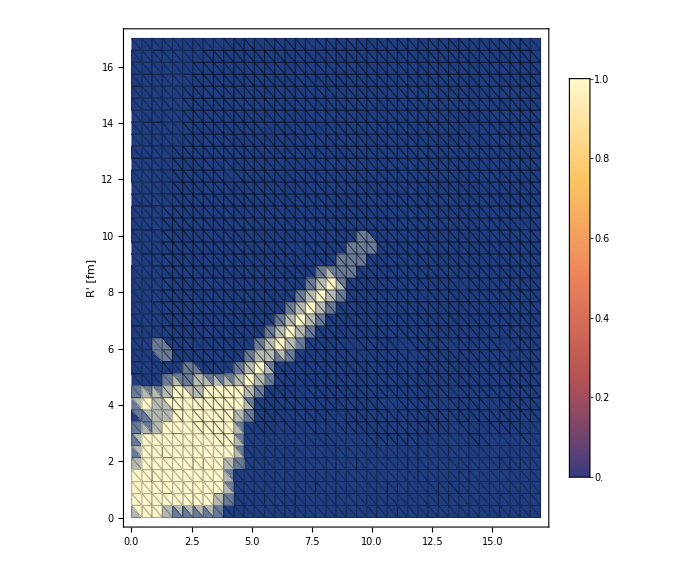
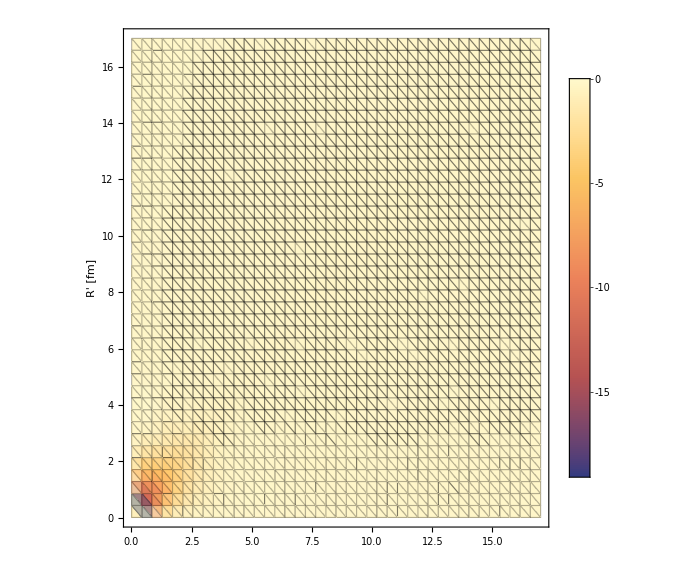
-Graphics- | -Graphics-

```mathematica
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=0.1,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```